```mathematica
file1 = SystemDialogInput["FileOpen"]
```

```mathematica
file1 = "K:\\Dropbox\\2012_04_16 PIDTune 001.csv"
```

K:\Dropbox\2012_04_16 PIDTune 001.csv

```mathematica
SystemDialogInput["FileOpen"]
```

```mathematica
file2 ="K:\\Dropbox\\2012_04_16 PIDTune 002.csv"
```

K:\Dropbox\2012_04_16 PIDTune 002.csv

```mathematica
file3 ="K:\\Dropbox\\2012_04_17 PIDTune 003.csv"
```

K:\Dropbox\2012_04_17 PIDTune 003.csv

```mathematica
file1
```

K:\Dropbox\2012_04_16 PIDTune 001.csv

```mathematica
file2
```

K:\Dropbox\2012_04_16 PIDTune 002.csv

```mathematica
"K:\\Dropbox\\2012_04_17 PIDTune 002.csv"
```

```mathematica
file3
```

K:\Dropbox\2012_04_17 PIDTune 003.csv

```mathematica
data1 = Import[file1]
```

{{Cooling profile},{},{Time,Downstream,Upstream,Inlet,Vb,dV,Heat pwr},{0.000000 Hz,3.3,10.000000 s},16489,{180.544,149.818,134.486,83.244,3.459,2.165,0.},{180.566,149.859,134.564,83.118,3.475,2.174,0.},{180.588,149.936,134.683,83.314,3.478,2.176,0.}}
 |  |  |  |

```mathematica
data2 = Import[file2]
```

{{Cooling profile},{},{Time,Downstream,Upstream,Inlet,Vb,dV,Heat pwr},{0.000000 Hz,3.3,10.000000 s},8667,{189.949,142.199,138.545,45.756,3.393,2.124,3.3},{189.971,142.501,138.607,45.947,3.393,2.124,3.3},{189.993,142.227,138.578,45.918,3.393,2.125,3.3}}
 |  |  |  |

```mathematica
data3 = Import[file3]
```

{{Cooling profile},{},{Time,Downstream,Upstream,Inlet,Vb,dV,Heat pwr},{0.000000 Hz,3.3,10.000000 s},24299,{180.531,150.254,143.178,43.937,3.522,2.233,3.},{180.554,149.879,142.905,43.765,3.502,2.22,3.},{180.576,149.794,143.046,43.826,3.549,2.251,3.}}
 |  |  |  |

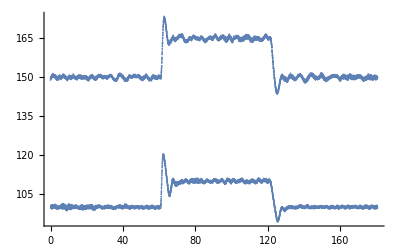

```mathematica
data1[[13;;All,{1,2}]]//ListPlot
```

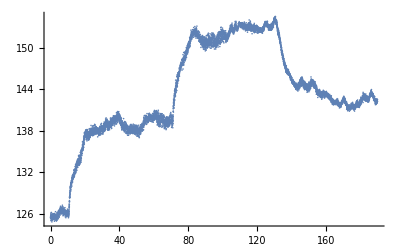

```mathematica
data2[[13;;All,{1,2}]]//ListPlot
```

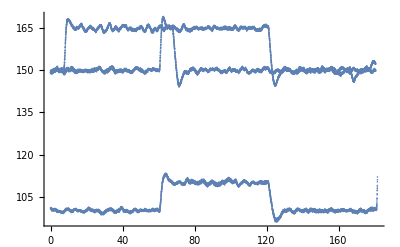

```mathematica
data3[[13;;All,{1,2}]]//ListPlot
```

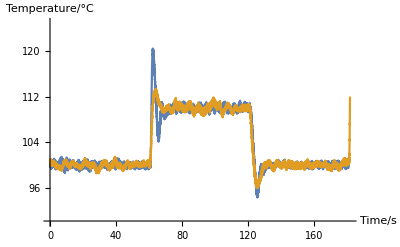

```mathematica
ListLinePlot[{data1[[13;;All,{1,2}]],data3[[13;;All,{1,2}]]}
	, PlotRange->{All,{90,125}}
	, AxesLabel->{"Time/s","Temperature/°C"}
]
```

```mathematica
spoint = {{0,100},{60,100},{60,110},{120,110},{120,100},{180,100}}
```

{{0,100},{60,100},{60,110},{120,110},{120,100},{180,100}}

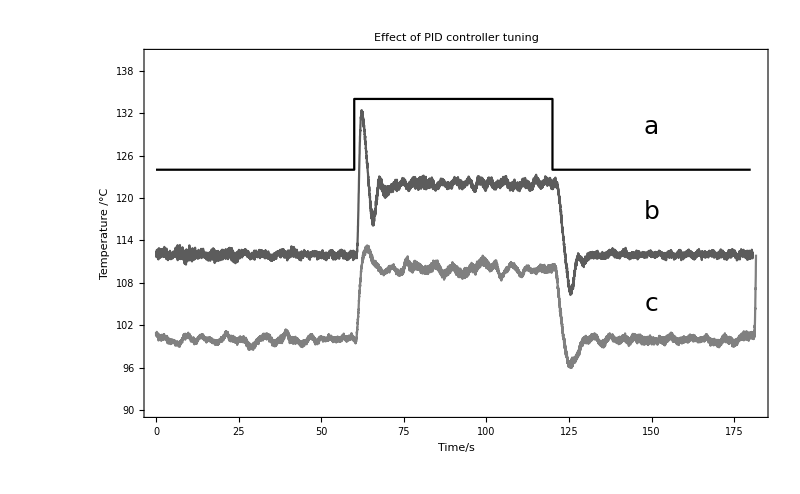

```mathematica
plot= ListLinePlot[{data3[[13;;All,{1,2}]]
		,data1[[13;;All,{1,2}]]+Table[{0,12}, Length[data1[[13;;All,{1,2}]]]]
		,spoint + Table[{0,24}, Length[spoint]]}
	, PlotStyle->{Gray, GrayLevel[0.36], Black}	
	, PlotLabel->Style["Effect of PID controller tuning", 30,Black,Bold ]
	,ImageSize-> 800 
	, Axes -> False
	, Frame->True
	, PlotRange->{All,{90,140}}
	, FrameLabel->{Style["Time/s", 25],Style["Temperature /°C", 25]}
	, FrameStyle->Directive[20, Black, Bold]
]; 
text ={Graphics[Text[Style["a", 25, Black],{150,130}]]
,Graphics[Text[Style["b", 25],{150,118}]]
,Graphics[Text[Style["c",25],{150,105}]]};
graph= Show[plot,text]
```

```mathematica
outfile = SystemDialogInput["FileSave"]
```

```mathematica
outfile = "C:\\Users\\fskdm\\My PhD\\Thesis\\Thesis For Erna\\Figures\\dev\\Loop tuning\\LoopTuningGraph.pdf"
```

C:\Users\fskdm\My PhD\Thesis\Thesis For Erna\Figures\dev\Loop tuning\LoopTuningGraph.pdf

```mathematica
Export[outfile, graph]
```

C:\Users\fskdm\My PhD\Thesis\Thesis For Erna\Figures\dev\Loop tuning\LoopTuningGraph.pdf